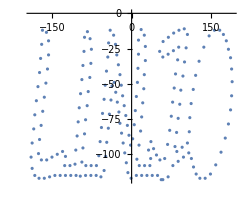

```mathematica
img=Import["G:\\my works new\\Illustrator\\for mathematica\\LINJO3.png"];
img=Binarize[img~ColorConvert~"Grayscale"~ImageResize~500~Blur~0.1];
pts=DeleteDuplicates@Cases[Normal@ListContourPlot[Reverse@ImageData[img],Contours->{0.5}],_Line,-1][[1,1]];
center=Mean@MinMax[pts]&/@Transpose@pts;
pts=#-center&/@pts[[;;;;20]];
elephantPlot=ListPlot[pts,AspectRatio->Automatic]
```

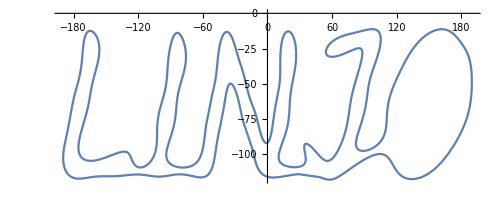

```mathematica
SetAttributes[toPt,Listable]
toPt[z_]:=ComplexExpand[{Re@z,Im@z}]//Chop;
cf=Compile[{{z,_Complex,1}},Module[{n=Length@z},1/n*Table[Sum[z[[k]]*Exp[-I*i*k*2 Pi/n],{k,1,n}],{i,-m,m}]]];
z=pts[[All,1]]+I*pts[[All,2]];
m=50;
cn=cf[z];
{f[t_],g[t_]}=Sum[cn[[j]]*Exp[I*(j-m-1)*t],{j,1,2 m+1}]//toPt;
ParametricPlot[{f[t],g[t]},{t,0,2 Pi},AspectRatio->Automatic]
```

```mathematica
r=Abs/@cn;
theta=Arg/@cn;
index={m+1}~Join~Riffle[Range[m+2,2 m+1],Reverse[Range[1,m]]];
p[t_]=Accumulate@Table[cn[[j]]*Exp[I*(j-m-1)*t],{j,index}]//toPt;
circles[t_]=Table[Circle[p[t][[i]],r[[index[[i]]]]],{i,1,2 m+1}];

anims=ParallelTable[ParametricPlot[{f[s],g[s]},{s,0,t},AspectRatio->Automatic,Epilog->{circles[t][[2;;]],Line[p[t]],Point[p[t]]},PlotRange->{{-200,200},{-200,0}},ImageSize->2000],{t,Subdivide[0.05,4 Pi,600]}];ListAnimate@anims
```

```mathematica
Export["LINJO6.avi",anims]
```

LINJO6.avi